# Functional Programing 2

## By Manuel Diaz, NTU, 2013.07.06 Following ideas from Mathematica Cookbook

## Doing simple mappings

#### Map[f,expr] == f /@ expr

```mathematica
Map[zz,{1,{1,2,3},{2,3,4}}]
```

{zz[1],zz[{1,2,3}],zz[{2,3,4}]}

we can also abbreviate this as:

```mathematica
zz /@{1,{1,2,3},{2,3,4}}
```

{zz[1],zz[{1,2,3}],zz[{2,3,4}]}

```mathematica
D[#, x] &/@ {{x^2,3x},x,{2 x},{1/x}}
```

{{2 x,3},1,{2},{-1/x^2}}

we can even map in a deeper level by doing

```mathematica
Map[zz,{1,{1,2,3},{2,3,4}},{2}]
```

{1,{zz[1],zz[2],zz[3]},{zz[2],zz[3],zz[4]}}

notice that the first element is not in the same level as the others.
we could also map elements in 1st  and second level at the same time:

```mathematica
Map[zz,{1,{1,2,3},{2,3,4}},2]
```

{zz[1],zz[{zz[1],zz[2],zz[3]}],zz[{zz[2],zz[3],zz[4]}]}

can you spot the difference? ... good!

#### Apply[f,expr] == f @@ expr

ok, now more systematic

```mathematica
list ={{a,b},1,{2,3,4}}
```

{{a,b},1,{2,3,4}}

```mathematica
list // FullForm
```

List[List[a,b],1,List[2,3,4]]

```mathematica
Map[Plus,list]
```

{{a,b},1,{2,3,4}}

uhm ... something is not right... we must tell mathematica that we want to Apply[] our choose fuction Plus[] as the header of each element in our list. First manually doing it:

```mathematica
{Plus[a,b],Plus[1],Plus[2,3,4]}
```

{a+b,1,9}

now using Map and Apply functions,

```mathematica
Map[(Apply[Plus, #]) & , list]
```

{a+b,1,9}

we can abbreviate this as:

```mathematica
Plus @@ # & /@ list
```

{a+b,1,9}

let’s do the cookbook example,

```mathematica
compOrderTotCost[qty_,price_]:=qty*price
compOrderTotCost @@ # & /@ {order[10,4.98],order[1,17.99],order[12,0.25]}
```

{49.8,17.99,3.}

```mathematica
compOrderTotCost @@ Rest[#] & /@ {order["sku1",10,4.98],order["sku1",1,17.99],order["sku1",12,0.25]}
```

{49.8,17.99,3.}

Here we have used Rest[] to remove the first element of the list

```mathematica
FullForm[{order["sku",1,2,]}]
```

List[order["sku",1,2,Null]]

```mathematica
Rest[{"sku",a,b}]
Rest[Rest[{"sku",a,b}]]
```

{a,b}

{b}

Observe that Apply does not necessarily need and expresion whose head is List

Doing it more dificult,

```mathematica
compDiscTotCost[qty_,price_,disc_]:=qty*price (1.0- disc/100.0)
compDiscTotCost[#3,#4,#2]& @@ #& /@ {order["sku1",5,10,4.98],order["sku2",0,1,17.99],order["sku2",15,12,0.25]}
```

{47.31,17.99,2.55}

There is another way to produce the same effect without explicitly using Map[],

```mathematica
Apply[Plus[##]&,list,1]
```

{a+b,1,9}

Yes, you got it, this is by using Apply[f,expr,1], that is forcing apply to work on the first level of headings!
a very compact way to do this is by doing,

### Apply[f,expr,1] == f @@@ expr

```mathematica
Plus @@@ list
```

{a+b,1,9}

we can even expand this for adding extra values to every term:

```mathematica
Plus[1,##]&@@@ list
```

{1+a+b,1,10}

uhm something failed with the 2nd term!!! ... recall

```mathematica
list //FullForm
```

List[List[a,b],1,List[2,3,4]]

here is the problem: the second term is has no header to be replaced! thus we have to do:

```mathematica
list = {{a,b},{1},{2,3,4}}
```

{{a,b},{1},{2,3,4}}

now everything will run perfectly:

```mathematica
Plus[1,##]&@@@ list
```

{1+a+b,2,10}

we can even add the second term in each list twice! of course we will get an error message becuase our second list has only 1 element,

```mathematica
Plus[#2,##]&@@@ list
```

Function::slotn: Slot number 2 in #2 + ##1 & cannot be filled from (#2 + ##1 &)[1].

{a+2 b,1+#2,12}

How about if the elements are deeply nested?

```mathematica
data = {envelope[1, order["sku1", 5, 10, 4.98]], envelope[2, order["sku1", 0, 1, 17.99]], envelope[3, order["sku1", 15, 12, 0.25]]};
```

```mathematica
data //TableForm
```

envelope[1,order[sku1,5,10,4.98]]
envelope[2,order[sku1,0,1,17.99]]
envelope[3,order[sku1,15,12,0.25]]

```mathematica
Map[Apply[compDiscTotCost[#3, #4, #2] &, #] &, data, {2}]
```

{envelope[1,47.31],envelope[2,17.99],envelope[3,2.55]}

Of course, we can discard the envelope. This is done with specification [[All,2]]

```mathematica
Map[Apply[compDiscTotCost[#3, #4, #2] &, #] &, data, {2}][[All, 2]]
```

{47.31,17.99,2.55}

## Creating functions that automatically Map over Lists

```mathematica
SetAttributes[myListableFunc,Listable]
myListableFunc[x_]:=x+1
myListableFunc[{1,2,3,4}]
```

{2,3,4,5}

Traditionally Log[] and D[] are built-in functions that are listable

```mathematica
Log[{0.01,0.1,1}]
```

{-4.60517,-2.30259,0}

```mathematica
D[{x,x^2,x^3,x^4},x]
```

{1,2 x,3 x^2,4 x^3}

Listability also works for operators used in prefix, infix and postfix notation

```mathematica
{10,20,30}^{3,2,1}
```

{1000,400,30}

```mathematica
{1/2,1/3,1/5,Sqrt[2]} //N
```

{0.5,0.333333,0.2,1.41421}

Listable has performance advantage over Map, so is recommendable if the function will offen be applied to vectors and matrices

```mathematica
RandomReal[{1,100}]
RandomReal[{1,100},1]
RandomReal[{1,100},2]
RandomReal[{1,100},{2,2}]
```

41.1782

{92.8852}

{25.5884,76.6877}

{{62.637,62.8297},{83.8761,99.1532}}

```mathematica
Timing[Log[RandomReal[{1,100},1000000]]][[1]]
```

0.212

```mathematica
Timing[Map[Log,RandomReal[{1,100},1000000]]][[1]]
```

0.556

## Mapping Multiple Functions in a Single Pass

now we are at the point where we can star thinking our way to map several functions over elements of a list in single pass.

```mathematica
{#,#^2,#^3}& /@ {1,7,3,8,5,9,4,2} //TableForm
```

1 | 1 | 1
7 | 49 | 343
3 | 9 | 27
8 | 64 | 512
5 | 25 | 125
9 | 81 | 729
4 | 16 | 64
2 | 4 | 8

```mathematica
Clear["data"]
data = Table[N[1/i π],{i,16,1,-1}];
data //TableForm
```

0.19635
0.20944
0.224399
0.241661
0.261799
0.285599
0.314159
0.349066
0.392699
0.448799
0.523599
0.628319
0.785398
1.0472
1.5708
3.14159

```mathematica
Sin[#]^2 +#Cos[2 #] & /@ data //TableForm
```

0.219464
0.23456
0.251693
0.271252
0.293712
0.319635
0.349652
0.384378
0.424127
0.468077
0.511799
0.539653
0.5
0.226401
-0.570796
3.14159

```mathematica
Table[With[{p = N[1/i π]}, Sin[p]^2 + p Cos[2 p]],{i,16,1,-1}] //TableForm
```

0.219464
0.23456
0.251693
0.271252
0.293712
0.319635
0.349652
0.384378
0.424127
0.468077
0.511799
0.539653
0.5
0.226401
-0.570796
3.14159

yes, but this last approach misses the point. Map applies to cases where the list is given an a new list with results must be generated. Table works best when you have to create a list on the fly.

```mathematica
Grid[Partition[RandomInteger[{1,10},100],20]]
```

10 | 2 | 8 | 8 | 4 | 6 | 5 | 3 | 7 | 8 | 9 | 7 | 5 | 7 | 7 | 5 | 2 | 7 | 10 | 2
9 | 8 | 3 | 7 | 10 | 9 | 5 | 7 | 2 | 4 | 2 | 1 | 1 | 5 | 3 | 3 | 8 | 10 | 9 | 8
3 | 1 | 7 | 3 | 3 | 9 | 8 | 7 | 4 | 3 | 7 | 4 | 7 | 5 | 9 | 9 | 6 | 7 | 10 | 8
5 | 3 | 9 | 5 | 8 | 9 | 10 | 1 | 9 | 5 | 4 | 7 | 5 | 3 | 2 | 3 | 6 | 4 | 3 | 4
8 | 2 | 8 | 4 | 6 | 1 | 7 | 3 | 3 | 2 | 7 | 4 | 9 | 8 | 10 | 6 | 1 | 1 | 10 | 2

```mathematica
Grid[Partition[Range[100],20]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

```mathematica
Grid[Partition[If[PrimeQ[#],Framed[#],#]&/@ Range[100],20]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

here another demostration

```mathematica
angles = Table[2 i π/n ,{n,3,14},{i,0,n-1}];
TableForm[angles,TableSpacing->{1/2,1}]
```

0 | (2 π)/3 | (4 π)/3 |  |  |  |  |  |  |  |  |  |  | 
0 | π/2 | π | (3 π)/2 |  |  |  |  |  |  |  |  |  | 
0 | (2 π)/5 | (4 π)/5 | (6 π)/5 | (8 π)/5 |  |  |  |  |  |  |  |  | 
0 | π/3 | (2 π)/3 | π | (4 π)/3 | (5 π)/3 |  |  |  |  |  |  |  | 
0 | (2 π)/7 | (4 π)/7 | (6 π)/7 | (8 π)/7 | (10 π)/7 | (12 π)/7 |  |  |  |  |  |  | 
0 | π/4 | π/2 | (3 π)/4 | π | (5 π)/4 | (3 π)/2 | (7 π)/4 |  |  |  |  |  | 
0 | (2 π)/9 | (4 π)/9 | (2 π)/3 | (8 π)/9 | (10 π)/9 | (4 π)/3 | (14 π)/9 | (16 π)/9 |  |  |  |  | 
0 | π/5 | (2 π)/5 | (3 π)/5 | (4 π)/5 | π | (6 π)/5 | (7 π)/5 | (8 π)/5 | (9 π)/5 |  |  |  | 
0 | (2 π)/11 | (4 π)/11 | (6 π)/11 | (8 π)/11 | (10 π)/11 | (12 π)/11 | (14 π)/11 | (16 π)/11 | (18 π)/11 | (20 π)/11 |  |  | 
0 | π/6 | π/3 | π/2 | (2 π)/3 | (5 π)/6 | π | (7 π)/6 | (4 π)/3 | (3 π)/2 | (5 π)/3 | (11 π)/6 |  | 
0 | (2 π)/13 | (4 π)/13 | (6 π)/13 | (8 π)/13 | (10 π)/13 | (12 π)/13 | (14 π)/13 | (16 π)/13 | (18 π)/13 | (20 π)/13 | (22 π)/13 | (24 π)/13 | 
0 | π/7 | (2 π)/7 | (3 π)/7 | (4 π)/7 | (5 π)/7 | (6 π)/7 | π | (8 π)/7 | (9 π)/7 | (10 π)/7 | (11 π)/7 | (12 π)/7 | (13 π)/7

We want to draw a polygon therefore we are requiered to compute their points by mapping the Sin and Cos function

```mathematica
Map[N[{Sin[#],Cos[#]}]&, angles,{2}][[1;;4]] //TableForm
```

0.
1. | 0.866025
-0.5 | -0.866025
-0.5 |  |  | 
0.
1. | 1.
0. | 0.
-1. | -1.
0. |  | 
0.
1. | 0.951057
0.309017 | 0.587785
-0.809017 | -0.587785
-0.809017 | -0.951057
0.309017 | 
0.
1. | 0.866025
0.5 | 0.866025
-0.5 | 0.
-1. | -0.866025
-0.5 | -0.866025
0.5

```mathematica
Map[N[{Sin[#],Cos[#]}]&, angles,{2}][[1;;4]]
```

{{{0.,1.},{0.866025,-0.5},{-0.866025,-0.5}},{{0.,1.},{1.,0.},{0.,-1.},{-1.,0.}},{{0.,1.},{0.951057,0.309017},{0.587785,-0.809017},{-0.587785,-0.809017},{-0.951057,0.309017}},{{0.,1.},{0.866025,0.5},{0.866025,-0.5},{0.,-1.},{-0.866025,-0.5},{-0.866025,0.5}}}

```mathematica
Degree==π/180
```

True

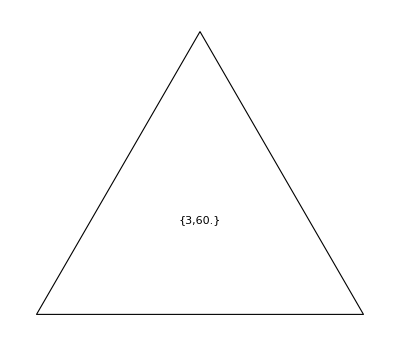
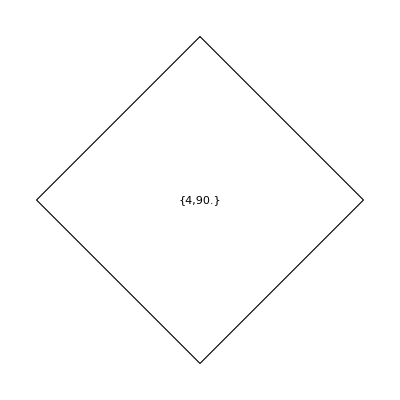
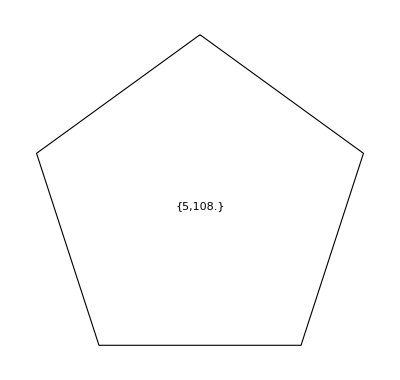
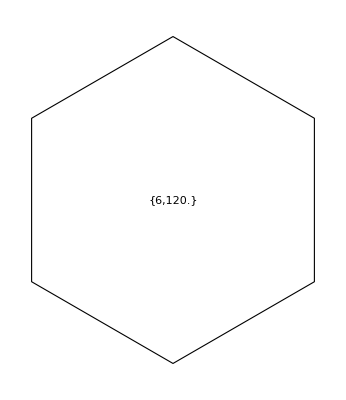

```mathematica
Graphics[{EdgeForm[{Thin,Black}],FaceForm[White],Polygon[#],Inset[{Length[#],(π-VectorAngle[#[[1]],#[[2]]])/Degree}]}]&/@ Map[N[{Sin[#],Cos[#]}]&, angles,{2}][[1;;4]]
```

## Defining Indexed Functions

You want to define a family of functions differentiated by an index or indices,

### use indexed heads

```mathematica
ClearAll[f];
f[1][x_,y_]:=0.5*(x+y)
f[2][x_,y_]:=0.5*(x-y)
f[3][x_,y_]:=0.5*(y-x)
```

```mathematica
Table[f[RandomInteger[{1,3}]][2,3],{i,6}]
```

{0.5,-0.5,0.5,-0.5,2.5,0.5}

### use subscrips

```mathematica
ClearAll[f];
Subscript[f, 1][x_,y_]:=0.5 (x+y)
Subscript[f, 2][x_,y_]:=0.5 (x-y)
Subscript[f, 3][x_,y_]:=0.5 (y-x)
```

```mathematica
Subscript[f, RandomInteger[{1,3}]][2,3]
```

0.5

### Stan Wagon’s example

```mathematica
Dot[{{x1,y1},{x2,y2}},{x,y}]+{a,b}
```

{a+x x1+y y1,b+x x2+y y2}

```mathematica
RandomChoice[{a,b,c},20]
```

{a,b,a,a,c,b,a,c,b,a,c,a,a,c,b,a,c,c,a,b}

```mathematica
RandomChoice[{a,b,c},{3,4}] //MatrixForm
```

(b | a | a | a
c | a | b | c
a | a | b | b)

Choices with weighted probabilities

```mathematica
RandomChoice[{0.1,0.2,0.7}->{a,b,c},20]
```

{c,c,c,c,c,c,c,b,c,a,c,b,c,c,b,b,c,c,c,c}

```mathematica
RandomChoice[{85,7,7,1}->{a,b,c,d},20]
```

{a,c,a,a,b,a,a,a,b,a,a,a,a,a,a,a,a,c,a,a}

```mathematica
NestList[zz,{0,0},5]
```

{{0,0},zz[{0,0}],zz[zz[{0,0}]],zz[zz[zz[{0,0}]]],zz[zz[zz[zz[{0,0}]]]],zz[zz[zz[zz[zz[{0,0}]]]]]}

```mathematica
Point /@ NestList[zz,{0,0},5]
```

{Point[{0,0}],Point[zz[{0,0}]],Point[zz[zz[{0,0}]]],Point[zz[zz[zz[{0,0}]]]],Point[zz[zz[zz[zz[{0,0}]]]]],Point[zz[zz[zz[zz[zz[{0,0}]]]]]]}

```mathematica
ClearAll[f];
f[a][{x_,y_}]:= Dot[{{0.85,0.04},{-0.04,0.85}},{x,y}]+{0,1.6}
f[b][{x_,y_}]:= Dot[{{-0.15,0.28},{0.26,0.24}},{x,y}]+{0,0.44}
f[c][{x_,y_}]:= Dot[{{0.2,-0.26},{0.23,0.22}},{x,y}]+{0,1.6}
f[d][{x_,y_}]:= Dot[{{0.0,0.0},{0.0,0.16}},{x,y}]
ff[p_]:=f[RandomChoice[{85,7,7,1}-> {a,b,c,d}]][p]
fern[n_]:=Graphics[{AbsolutePointSize[0.5],Point /@ NestList[ff,{0,0.05},n]}, PlotRangePadding->{{-1,1},{-1,1}},AspectRatio->0.9,ImageSize->Small]
```

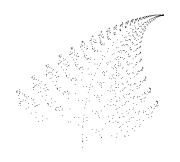

```mathematica
fern[1000]
```

## Understanding the use of Fold as an alternative to Recursion

You want to understand and create programs that use Fold[] as an alternative to explicit recursion,

```mathematica
Fold[zz,x,{a,1,2,3,4}]
```

zz[zz[zz[zz[zz[x,a],1],2],3],4]

```mathematica
Fold[##&,0,{a,1,2,3,4}]
```

Sequence[0,a,1,2,3,4]

```mathematica
Fold[Plus[##]&,x,{a,1,2,3,4}]
```

10+a+x

```mathematica
Fold[Plus,x,order[a,1,2,3,4]]
```

10+a+x

The head doesn’t needs to be a List type.

```mathematica
Plus[x,{a,1,2,3,4}]
```

{a+x,1+x,2+x,3+x,4+x}

```mathematica
Plus[{x,a,1,2,3,4}]
```

{x,a,1,2,3,4}

```mathematica
Plus[x,a,1,2,3,4]
```

10+a+x

Well here I recognize that if I want to perform the sumatory of the elements in my list and add something extra only Plus function cannot help me .

Here I’m trying to compare to what I learned before,

```mathematica
Map[Apply [Plus, #] &,{a,1,2,3,4}]
```

{a,1,2,3,4}

```mathematica
Plus @@ # & /@ {a,1,2,3,4}
```

{a,1,2,3,4}

yes, here can be notizable that what we have been learning use usefull for nested lists.

### Fold for creating nexted polynomials

```mathematica
Fold[x #1 +#2 &,0,{a,b,c,d,e}]
```

e+x (d+x (c+x (b+a x)))

### continuous fraction

```mathematica
Fold[1/(#2+#1)&,0,{a,b,c,d,e}]
```

1/(1/(1/(1/(1/a+b)+c)+d)+e)

```mathematica
Fold[1/(#2+#1)&,0,Reverse[{a,b,c,d}]]
```

1/(a+1/(b+1/(c+1/d)))

```mathematica
Fold[1/(#2+#1)&,x,Reverse[{a,b,c,d}]]
```

1/(a+1/(b+1/(c+1/(d+x))))

Observe that ‘x’ is added at the very end of the fold operation.

### Form an alternating sum

```mathematica
Fold[#2-#1&,0,Reverse[{a,b,c,d,e}]]
```

a-b+c-d+e

### Finally for recurrences

```mathematica
First[{a,b,c,d,e}]
```

a

```mathematica
Last[{a,b,c,d,e}]
```

e

```mathematica
Rest[{a,b,c,d,e}]
```

{b,c,d,e}

```mathematica
Most[{a,b,c,d,e}]
```

{a,b,c,d}

```mathematica
Take[{a,b,c,d,e},3]
```

{a,b,c}

```mathematica
Drop[{a,b,c,d,e},3]
```

{d,e}

```mathematica
Select[{0,1,2,3,4,5,6},EvenQ]
```

{0,2,4,6}

Traditional form as found in the Cookbook

```mathematica
mySum[{}]:=0
mySum[l_]:=First[l]+mySum[Rest[l]]
```

```mathematica
mySum[{1,2,3,4,5}]
```

15

```mathematica
mySum[{2,a,v}]
```

2+a+v

now using Fold[]

```mathematica
mySum2[l_]:=Fold[#2+#1&,0,l]
```

```mathematica
mySum2[{1,2,3,4,5}]
```

15

```mathematica
mySum2[{2,a,c}]
```

2+a+c

## Computing through repeated function application

You want to understand the types of computations you can perform using the Nest family of functions (Nest, NestList, NestWhile, NestWhileList)

## Building a Function through Iteration